## Solving with knowns: mdot, α, constant κR

```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
dirName="/home/dan/ResearchLocal/"
SetDirectory[dirName];
```

/home/dan/ResearchLocal/

SetDirectory::cdir: Cannot set current directory to /home/dan/ResearchLocal/.

```mathematica
eqTab={
ν==α cs h,
cs^2==(kb Tc)/(μ mp),
ρ==1/(√(2 π))Σ/h,
h==cs/Ω,
Tc^4==3/4 τ Tdisk^4,
τ==1/2 Σ κR,
ν Σ==mdot/(3π),
σ Tdisk^4==9/8 ν Σ Ω^2,
κR==κR0,
α==b1*β^(-1/2),
β==(ρ cs^2)/B^2
};
Length[eqTab]
```

11

```mathematica
unknowns={Tc,Tdisk,cs,ρ,h,κR,ν,τ,Σ,α};
knownsFuncs={Ω};
constants={kb,μ,mp,G,M,σ,mdot};
```

```mathematica
rulesTab={ν>0,α>0,cs>0,h>0,kb>0,Tc>0,μ>0,mp>0,ρ>0,Σ>0,Ω>0,τ>0,Tdisk>0,τ>0,mdot>0,σ>0,κR>0,κR0>0,Tc>0,β>0,B>0,b1>0};
```

```mathematica
sol1=Solve[Flatten[{eqTab,rulesTab}],{Tc,Tdisk,cs,ρ,h,κR,ν,τ,Σ,β,α},Reals];
```

```mathematica
sol2=Reduce[Flatten[{eqTab,rulesTab}],{Tc,Tdisk,cs,ρ,h,κR,ν,τ,Σ,β,α},Reals];
```

```mathematica
sol2Tab=Table[sol2[[i]],{i,1,20}]//TableForm
```

Ω>0
σ>0
μ>0
κR0>0
mp>0
mdot>0
kb>0
b1>0
B>0
Tc==Root[-mdot^6 mp^3 κR0^2 μ^3 Ω^10+8192 B^4 b1^4 kb^3 π^7 σ^2 #1^11&,1]
Tdisk==Root[-3 mdot Ω^2+8 π σ #1^4&,2]
cs==√((kb Tc)/(mp μ))
ρ==(4 √(2/π) Tc^4 Ω)/(3 cs Tdisk^4 κR0)
h==cs/Ω
κR==(4 √(2/π) Tc^4)/(3 h Tdisk^4 ρ)
ν==mdot/(3 √2 h π^(3/2) ρ)
τ==(4 Tc^4)/(3 Tdisk^4)
Σ==h √(2 π) ρ
β==(cs^2 ρ)/B^2
α==ν/(cs h)

```mathematica
mp=1;μ=1;kb=1;mdot=1;κR0=1;mp=1;σ=1;b1=11;
```

```mathematica
Table[{sol1[[1,i,1]],sol1[[1,i,2,1]]},{i,1,11}]//TableForm;
```

```mathematica
B0=10^-6;Bindex=-1/2;
```

```mathematica
Table[
{sol1[[1,i,1]],
Log10[(sol1[[1,i,2,1]]/.{Ω->r^(-3/2),B->B0*r^Bindex}/.{r->10})/(sol1[[1,i,2,1]]/.{Ω->r^(-3/2),B->B0*r^Bindex}/.{r->1})]//Rationalize,
Log10[(sol1[[1,i,2,1]]/.{Ω->r^(-3/2),B->B0*r^Bindex}/.{r->10})/(sol1[[1,i,2,1]]/.{Ω->r^(-3/2),B->B0*r^Bindex}/.{r->1})]//N
},
{i,1,11}]//TableForm
```

Tc | Log[Root[-4000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]/(10000 Root[-400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1])]/Log[10] | -1.18182
Tdisk | Log[Root[-3+8000 π #1^4&,2]/Root[-3+8 π #1^4&,2]]/Log[10] | -0.75
cs | Log[1/100 √(Root[-4000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]/Root[-400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1])]/Log[10] | -0.590909
ρ | Log[(1000 Root[-400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]^2)/(Root[-4000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]^2)]/Log[10] | -2.63636
h | -Log[(10 Root[-400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1])/Root[-4000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]]/(2 Log[10]) | 0.909091
κR | Log[(Root[-3+8 π #1^4&,2]^4 (Root[-4000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]/Root[-400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1])^(11/2))/(1000000000000000000 √10 Root[-3+8000 π #1^4&,2]^4)]/Log[10] | 5.78596×10^-16
ν | Log[((Root[-4000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]/Root[-400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1])^(3/2))/(100 √10)]/Log[10] | 1.72727
τ | Log[(Root[-3+8 π #1^4&,2]^4 Root[-4000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]^4)/(10000000000000000 Root[-3+8000 π #1^4&,2]^4 Root[-400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]^4)]/Log[10] | -1.72727
Σ | Log[100 √10 (Root[-400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]/Root[-4000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1])^(3/2)]/Log[10] | -1.72727
β | Log[Root[-400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]/Root[-4000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]]/Log[10] | -2.81818
α | Log[Root[-4000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]/Root[-400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+174476096635810856063687350929 π^26 #1^11&,1]]/(2 Log[10]) | 1.40909

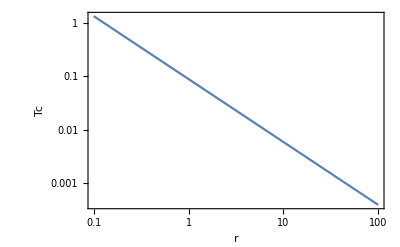
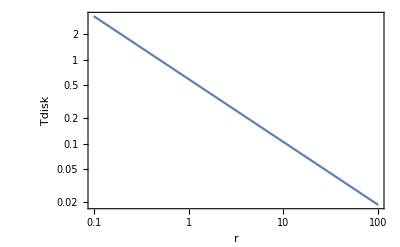
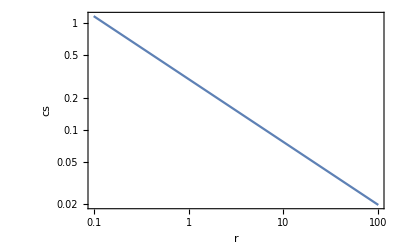
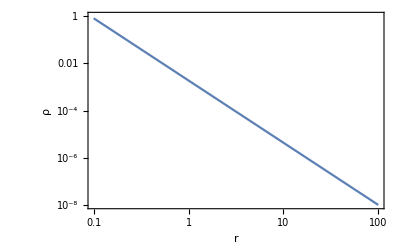
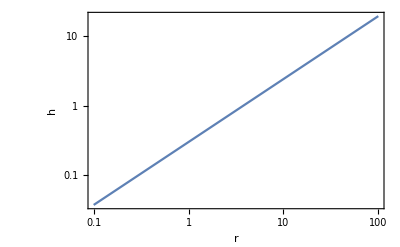
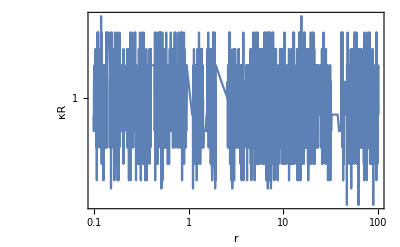
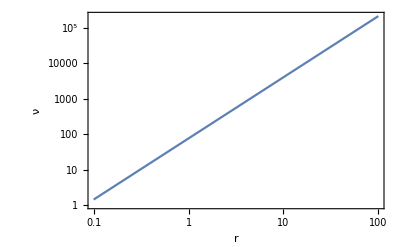
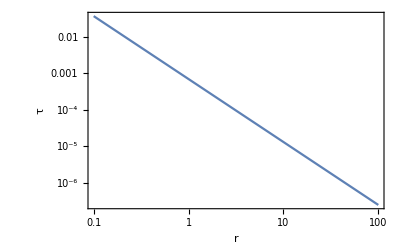

```mathematica
Table[
LogLogPlot[sol1[[1,i,2,1]]/.{Ω->r^(-3/2),B->r^(-1/2)}//N,{r,0.1,100},
Frame->True,
FrameLabel->{"r",sol1[[1,i,1]]}],
{i,1,11}]
```